```mathematica
P1=Import["P1.txt","Table"];
P2=Import["P2.txt","Table"];
```

```mathematica
Clear[V0];
μ=50;
nn=9;
wc=μ/(nn+1);
(*Ez=(3/4)*wc;*)
{Ez,me}={0.9*wc,1};
data={};
(*x1=(2-(1-α)*Vp)*4*α*Vp/(((1-α)*Vp)*(2-(1+3*α)))/.Vp->0.01*)
(*x2=(2-(1-α)*Vp)*4*α*Vp/(((1-α)*Vp)*(2-(1+3*α)))/.Vp->π*)
l=1/Sqrt[me*wc];
kf[n_,s_]:=Re[Sqrt[2*me*(μ-((n+1/2)*wc-Sign[s]*Ez/2))]];
(*sn[n_,m_]:=(-1/Pi)*(1/l)*(kf[m,-1]*P1[[n+1,m+1]]-kf[m,+1]*P1[[n+2,m+1]]);*)
sn[n_,m_]:=(1/π)*(1/l)*(kf[m,+1]*P1[[n+1,m+1]]-kf[m,-1]*P1[[n+2,m+1]]);
s[n_]:=Sum[sn[n,m],{m,0,nn+1}];
sm[n_,m_]:=Piecewise[{{s[n],n==m}},0];
smatrix=Table[sm[n,m],{n,0,nn},{m,0,nn}];
km[n_,m_]:=Piecewise[{{(1/Pi)*(kf[n,-1]-kf[n+1,+1]),n==m}},0];kmatrix=Table[km[n,m],{n,0,nn},{m,0,nn}];
vmatrix=Table[(1/l)*P2[[n+1,m+1]],{n,0,nn},{m,0,nn}];
M=-kmatrix.vmatrix-smatrix;
Mx=Eigenvalues[M];
For[V0=0.0,V0≤π,V0+=0.05,
{For[i=0,i≤nn,i++,
{mm=Mx[[i+1]];
ω=V0*mm+(wc-Ez);
AppendTo[data,{V0*me/π,ω/wc}]}];
}]
```

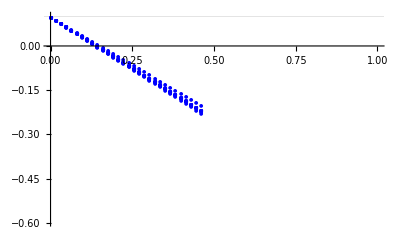

```mathematica
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},Automatic},PlotMarkers->{Automatic,5},GridLines->{None,{{(1-Ez/wc),{AbsoluteDashing[{13,10}],Thick,Black}}}},PlotLabel->"N=10"]
```

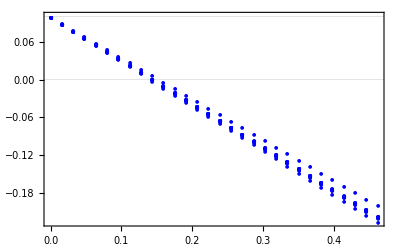

```mathematica
x={0.15,-0.8};y=Table[-10+.5*i,{i,0,200}];
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},Frame->{True,True,True,True},GridLines->{None,{{(1-Ez/wc),{AbsoluteDashing[{13,10}],Thickness[0.01],Black}},{0,{Thickness[0.01],Black}}}},FrameLabel->{"(V̄)/π","ω/ω_c",None,None},FrameTicks->{{0,0.5,1},y,None,None},PlotMarkers->{Automatic,5}]
```

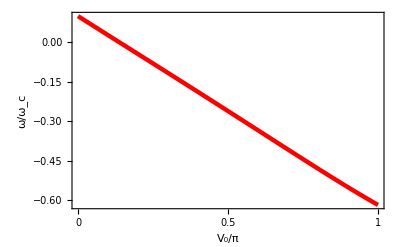

```mathematica
f2=Plot[-(1/wc)*(Ez+(p*Ez)/(4*(1-p/2))-√((p^2 Ez^2)/(16(1-p/2)^2)+wc^2*((1-p/2)/(1+p/2)))),{p,0,1},PlotRange->x,PlotStyle->{Thickness[0.008],Red},Frame->{True,True,True,True},FrameLabel->{"V_0/π","ω/ω_c",None,None},FrameTicks->{{0,0.5,1},Automatic,None,None}]
```

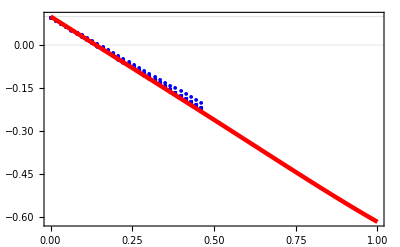

```mathematica
Export["Ez=0-9wc_nn=9_H.png",Show[f1,f2,Frame->{True,True,True,True},FrameLabel->{"(V̄)/π",None,None,None},LabelStyle->Directive[Black,20],FrameTicks->{{0,0.5,1},y,None,None}],ImageResolution->600,ImageSize->{430,304}];
Show[f1,f2]
```

```mathematica
(*ImageSize->{430,304}*)
```

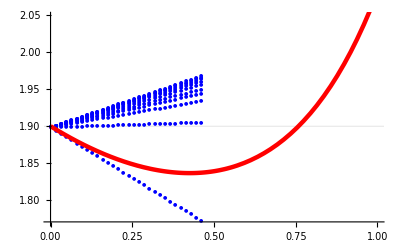

```mathematica
Show[f1,f2]
```

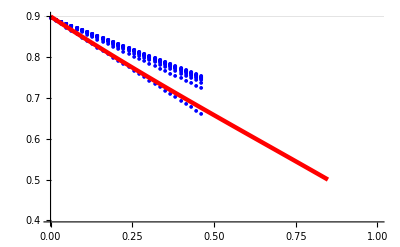

```mathematica
Show[f1,f2]
```

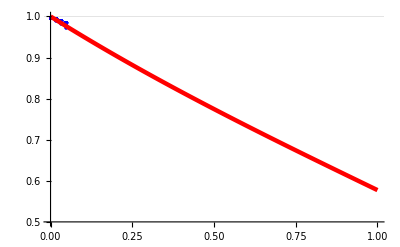

```mathematica
Show[f1,f2]
```

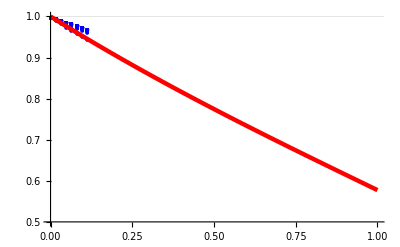

```mathematica
Show[f1,f2]
```

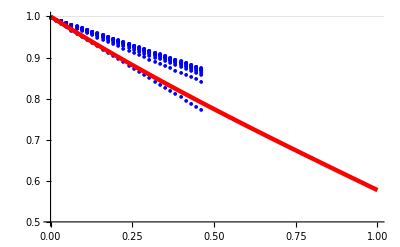

```mathematica
Show[f1,f2]
```

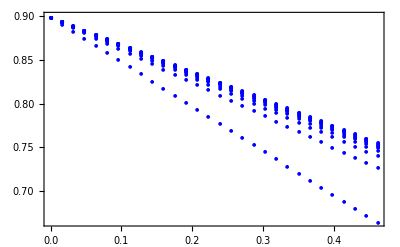

```mathematica
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},Frame->{True,True,True,True},FrameLabel->{"(V̄)/π","ω/ω_c",None,None},FrameTicks->{{0,0.5,1},y,None,None},PlotMarkers->{Automatic,5}]
```